```mathematica
(* pie chart in Fig 1D *)
(* Sevahn Vorperian, Quake Lab *)
```

```mathematica
(* copying everything over here that is working because other notebook is a mess *)
```

```mathematica
fractions = Import["/Users/kayaneh/Documents/deconvolution/revision1/08012021_perComp_noEye_sigmat_18/adnci_v18_rmseAll_11282021/UniversityofWashingtonatSt.Louis_sigMat18_avgCoefs_plasma_1129021.csv"];
```

```mathematica
roundPower = 0.1;
percentThresh = 1; (* percentage cutoff for stacked bar chart vs main pie *)
scalePercents = 100; (* scale all percentages by 100 *)
superSmallThresh = 0.1; (* percentage cutoff for cell types with small fractional contirbutions *)
sampleCenter = "University of Washington at St. Louis";
```

```mathematica
fractions
```

{{,University of Washington at St. Louis},{erythrocyte/erythroid progenitor,0.443796},{platelet,0.104313},{monocyte,0.0779122},{nk cell,0.0464626},{b cell,0.0407815},{basophil,0.032406},{mature conventional dendritic cell,0.0284612},{endothelial cell,0.0273598},{neutrophil,0.0203169},{cell of skeletal muscle,0.0191728},{adventitial cell,0.016907},{thymocyte,0.0137956},{intestinal tuft cell,0.0135775},{salivary/bronchial secretory cell,0.0119142},{macrophage,0.00887319},{kidney epithelial cell,0.00852469},{medullary thymic epithelial cell,0.0085227},{intestinal enterocyte,0.00730452},{salivary gland cell,0.00695053},{basal cell,0.0066551},{pancreatic stellate cell,0.00610877},{myeloid progenitor,0.00581391},{respiratory ciliated cell,0.00562082},{intrahepatic cholangiocyte,0.00521858},{intestinal secretory cell,0.00480439},{ionocyte/luminal epithelial cell of mammary gland,0.00426548},{pericyte cell,0.00359674},{schwann cell,0.00314482},{secretory cell,0.00285058},{pancreatic alpha/beta cell,0.00257171},{type ii pneumocyte,0.00237296},{t cell,0.00151959},{respiratory secretory cell,0.00136238},{prostate epithelia,0.00114346},{basal cell of prostate epithelium,0.00100194},{plasma cell,0.00099859},{mesothelial cell,0.000620595},{pancreatic ductal cell,0.000518163},{plasmablast,0.000514075},{goblet cell,0.000365427},{innate lymphoid cell,0.000244456},{pancreatic delta cell,0.000218241},{club cell/type i pneumocyte,0.000200074},{pancreatic acinar cell,0.000179262},{pancreatic pp cell,0.000147054},{hematopoietic stem cell,0.000135551},{bladder urothelial cell,0.000128051},{stromal cell,0.000104141},{tendon cell,0.0000615745},{melanocyte,0.0000597792},{cardiac muscle cell,0.0000525442},{hepatocyte,0.0000459976},{fibroblast/mesenchymal stem cell,3.09296×10^-6}}

```mathematica
fractions = fractions[[2;;]]; (* eliminate the center name *)
```

```mathematica
(* cellTypes = fractions[[1]][[2;;]] *)
cellTypes = fractions[[;;,1]]
```

{erythrocyte/erythroid progenitor,platelet,monocyte,nk cell,b cell,basophil,mature conventional dendritic cell,endothelial cell,neutrophil,cell of skeletal muscle,adventitial cell,thymocyte,intestinal tuft cell,salivary/bronchial secretory cell,macrophage,kidney epithelial cell,medullary thymic epithelial cell,intestinal enterocyte,salivary gland cell,basal cell,pancreatic stellate cell,myeloid progenitor,respiratory ciliated cell,intrahepatic cholangiocyte,intestinal secretory cell,ionocyte/luminal epithelial cell of mammary gland,pericyte cell,schwann cell,secretory cell,pancreatic alpha/beta cell,type ii pneumocyte,t cell,respiratory secretory cell,prostate epithelia,basal cell of prostate epithelium,plasma cell,mesothelial cell,pancreatic ductal cell,plasmablast,goblet cell,innate lymphoid cell,pancreatic delta cell,club cell/type i pneumocyte,pancreatic acinar cell,pancreatic pp cell,hematopoietic stem cell,bladder urothelial cell,stromal cell,tendon cell,melanocyte,cardiac muscle cell,hepatocyte,fibroblast/mesenchymal stem cell}

```mathematica
(* fractions =fractions[[2;;,2;;]][[1]] *)
fractions = fractions[[;;,2]]
```

{0.443796,0.104313,0.0779122,0.0464626,0.0407815,0.032406,0.0284612,0.0273598,0.0203169,0.0191728,0.016907,0.0137956,0.0135775,0.0119142,0.00887319,0.00852469,0.0085227,0.00730452,0.00695053,0.0066551,0.00610877,0.00581391,0.00562082,0.00521858,0.00480439,0.00426548,0.00359674,0.00314482,0.00285058,0.00257171,0.00237296,0.00151959,0.00136238,0.00114346,0.00100194,0.00099859,0.000620595,0.000518163,0.000514075,0.000365427,0.000244456,0.000218241,0.000200074,0.000179262,0.000147054,0.000135551,0.000128051,0.000104141,0.0000615745,0.0000597792,0.0000525442,0.0000459976,3.09296×10^-6}

```mathematica
Length[fractions]
```

53

```mathematica
Length[cellTypes]
```

53

```mathematica
(* fractions = Import["~/Documents/deconvolution/cellTypeFractions_10XDecon_07222020.xlsx"][[1]]; *)
```

```mathematica
contribs = fractions  (* excluded sample name and r, p-value, RMSE *)
```

{0.443796,0.104313,0.0779122,0.0464626,0.0407815,0.032406,0.0284612,0.0273598,0.0203169,0.0191728,0.016907,0.0137956,0.0135775,0.0119142,0.00887319,0.00852469,0.0085227,0.00730452,0.00695053,0.0066551,0.00610877,0.00581391,0.00562082,0.00521858,0.00480439,0.00426548,0.00359674,0.00314482,0.00285058,0.00257171,0.00237296,0.00151959,0.00136238,0.00114346,0.00100194,0.00099859,0.000620595,0.000518163,0.000514075,0.000365427,0.000244456,0.000218241,0.000200074,0.000179262,0.000147054,0.000135551,0.000128051,0.000104141,0.0000615745,0.0000597792,0.0000525442,0.0000459976,3.09296×10^-6}

```mathematica
Length[fractions]
```

53

```mathematica
Length[cellTypes]
```

53

```mathematica
(* first get the zero index *)
```

```mathematica
zeroIndex = Position[contribs, val_/;val ≤ 0]
```

{}

```mathematica
(* drop it from the contributions and drop the corresponding labels *)
```

```mathematica
nonZeroVals = Delete[contribs, zeroIndex];
```

```mathematica
nonZeroVals = nonZeroVals * scalePercents
```

{44.3796,10.4313,7.79122,4.64626,4.07815,3.2406,2.84612,2.73598,2.03169,1.91728,1.6907,1.37956,1.35775,1.19142,0.887319,0.852469,0.85227,0.730452,0.695053,0.66551,0.610877,0.581391,0.562082,0.521858,0.480439,0.426548,0.359674,0.314482,0.285058,0.257171,0.237296,0.151959,0.136238,0.114346,0.100194,0.099859,0.0620595,0.0518163,0.0514075,0.0365427,0.0244456,0.0218241,0.0200074,0.0179262,0.0147054,0.0135551,0.0128051,0.0104141,0.00615745,0.00597792,0.00525442,0.00459976,0.000309296}

```mathematica
Total[nonZeroVals]
```

100.

```mathematica
nonZeroCells = Delete[cellTypes, zeroIndex];
```

```mathematica
Length[nonZeroCells]
```

53

```mathematica
nonZeroCells
```

{erythrocyte/erythroid progenitor,platelet,monocyte,nk cell,b cell,basophil,mature conventional dendritic cell,endothelial cell,neutrophil,cell of skeletal muscle,adventitial cell,thymocyte,intestinal tuft cell,salivary/bronchial secretory cell,macrophage,kidney epithelial cell,medullary thymic epithelial cell,intestinal enterocyte,salivary gland cell,basal cell,pancreatic stellate cell,myeloid progenitor,respiratory ciliated cell,intrahepatic cholangiocyte,intestinal secretory cell,ionocyte/luminal epithelial cell of mammary gland,pericyte cell,schwann cell,secretory cell,pancreatic alpha/beta cell,type ii pneumocyte,t cell,respiratory secretory cell,prostate epithelia,basal cell of prostate epithelium,plasma cell,mesothelial cell,pancreatic ductal cell,plasmablast,goblet cell,innate lymphoid cell,pancreatic delta cell,club cell/type i pneumocyte,pancreatic acinar cell,pancreatic pp cell,hematopoietic stem cell,bladder urothelial cell,stromal cell,tendon cell,melanocyte,cardiac muscle cell,hepatocyte,fibroblast/mesenchymal stem cell}

```mathematica
nonZeroVals
```

{44.3796,10.4313,7.79122,4.64626,4.07815,3.2406,2.84612,2.73598,2.03169,1.91728,1.6907,1.37956,1.35775,1.19142,0.887319,0.852469,0.85227,0.730452,0.695053,0.66551,0.610877,0.581391,0.562082,0.521858,0.480439,0.426548,0.359674,0.314482,0.285058,0.257171,0.237296,0.151959,0.136238,0.114346,0.100194,0.099859,0.0620595,0.0518163,0.0514075,0.0365427,0.0244456,0.0218241,0.0200074,0.0179262,0.0147054,0.0135551,0.0128051,0.0104141,0.00615745,0.00597792,0.00525442,0.00459976,0.000309296}

```mathematica
(* nonZeroVals = nonZeroVals/Total[nonZeroVals] (* normalize to 1 *) did this normalization in python *)
```

```mathematica
nonZeroVals = Round[#, roundPower] &/@nonZeroVals (* round to 3 digits *)
```

{44.4,10.4,7.8,4.6,4.1,3.2,2.8,2.7,2.,1.9,1.7,1.4,1.4,1.2,0.9,0.9,0.9,0.7,0.7,0.7,0.6,0.6,0.6,0.5,0.5,0.4,0.4,0.3,0.3,0.3,0.2,0.2,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Total[nonZeroVals]
```

100.

```mathematica
(* get index cell types that are less than one percent together for the bar chart *)
```

```mathematica
lt1Percent = Position[nonZeroVals, val_/;val  < percentThresh]
```

{{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27},{28},{29},{30},{31},{32},{33},{34},{35},{36},{37},{38},{39},{40},{41},{42},{43},{44},{45},{46},{47},{48},{49},{50},{51},{52},{53}}

```mathematica
(* now pull the cell types and their associated values and put in reverse order so it goes from smallest to largest *)
```

```mathematica
smallContribVals = Reverse[Part[nonZeroVals, # ]&/@ lt1Percent]
smallContribCells = Reverse[Part[nonZeroCells, #] &/@ lt1Percent];
```

{{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.1},{0.1},{0.1},{0.1},{0.1},{0.1},{0.1},{0.2},{0.2},{0.3},{0.3},{0.3},{0.4},{0.4},{0.5},{0.5},{0.6},{0.6},{0.6},{0.7},{0.7},{0.7},{0.9},{0.9},{0.9}}

```mathematica
(* get the indices where the elements are ≤ 0.1% or 0.001 *)
```

```mathematica
ltPt1Percent = Position[Flatten[smallContribVals], val_/;val  ≤ superSmallThresh]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21}}

```mathematica
(* get the sum of the values and the respective cell ≤ 0.1 % *)
fracsLTPt1 = Part[smallContribVals, # ] &/@ ltPt1Percent
cellsLTPt1 = Part[smallContribCells, #] &/@ ltPt1Percent
```

{{{0.}},{{0.}},{{0.}},{{0.}},{{0.}},{{0.}},{{0.}},{{0.}},{{0.}},{{0.}},{{0.}},{{0.}},{{0.}},{{0.}},{{0.1}},{{0.1}},{{0.1}},{{0.1}},{{0.1}},{{0.1}},{{0.1}}}

{{{fibroblast/mesenchymal stem cell}},{{hepatocyte}},{{cardiac muscle cell}},{{melanocyte}},{{tendon cell}},{{stromal cell}},{{bladder urothelial cell}},{{hematopoietic stem cell}},{{pancreatic pp cell}},{{pancreatic acinar cell}},{{club cell/type i pneumocyte}},{{pancreatic delta cell}},{{innate lymphoid cell}},{{goblet cell}},{{plasmablast}},{{pancreatic ductal cell}},{{mesothelial cell}},{{plasma cell}},{{basal cell of prostate epithelium}},{{prostate epithelia}},{{respiratory secretory cell}}}

```mathematica
totalSuperSmall = Total[Flatten[fracsLTPt1]]
```

0.7

```mathematica
(* now drop those small guys *)
```

```mathematica
goodSmallVals = Delete[smallContribVals, ltPt1Percent];
goodSmallCells = Delete[smallContribCells, ltPt1Percent];
```

```mathematica
goodSmallCells
```

{{t cell},{type ii pneumocyte},{pancreatic alpha/beta cell},{secretory cell},{schwann cell},{pericyte cell},{ionocyte/luminal epithelial cell of mammary gland},{intestinal secretory cell},{intrahepatic cholangiocyte},{respiratory ciliated cell},{myeloid progenitor},{pancreatic stellate cell},{basal cell},{salivary gland cell},{intestinal enterocyte},{medullary thymic epithelial cell},{kidney epithelial cell},{macrophage}}

```mathematica
(* add the sum of the remaining cells *)
goodSmallVals = AppendTo[goodSmallVals, {totalSuperSmall}]
goodSmallCells = AppendTo[goodSmallCells, {"Very Small Contributors"}]
```

{{0.2},{0.2},{0.3},{0.3},{0.3},{0.4},{0.4},{0.5},{0.5},{0.6},{0.6},{0.6},{0.7},{0.7},{0.7},{0.9},{0.9},{0.9},{0.7}}

{{t cell},{type ii pneumocyte},{pancreatic alpha/beta cell},{secretory cell},{schwann cell},{pericyte cell},{ionocyte/luminal epithelial cell of mammary gland},{intestinal secretory cell},{intrahepatic cholangiocyte},{respiratory ciliated cell},{myeloid progenitor},{pancreatic stellate cell},{basal cell},{salivary gland cell},{intestinal enterocyte},{medullary thymic epithelial cell},{kidney epithelial cell},{macrophage},{Very Small Contributors}}

```mathematica
(* now sort this finalized "small cell" list *)
```

```mathematica
finalOrder = Reverse[Ordering[goodSmallVals]]
```

{18,17,16,15,14,13,19,12,11,10,9,8,7,6,5,4,3,2,1}

```mathematica
goodSmallVals = Flatten[Part[goodSmallVals , #] &/@ finalOrder]
```

{0.9,0.9,0.9,0.7,0.7,0.7,0.7,0.6,0.6,0.6,0.5,0.5,0.4,0.4,0.3,0.3,0.3,0.2,0.2}

```mathematica
goodSmallCells = Flatten[Part[goodSmallCells, #] &/@ finalOrder]
```

{macrophage,kidney epithelial cell,medullary thymic epithelial cell,intestinal enterocyte,salivary gland cell,basal cell,Very Small Contributors,pancreatic stellate cell,myeloid progenitor,respiratory ciliated cell,intrahepatic cholangiocyte,intestinal secretory cell,ionocyte/luminal epithelial cell of mammary gland,pericyte cell,schwann cell,secretory cell,pancreatic alpha/beta cell,type ii pneumocyte,t cell}

```mathematica
(* now make the bar chart *)
```

```mathematica
shortlist =List[Flatten[Table[Callout[goodSmallVals[[#]], goodSmallCells[[#]],After,Appearance->"Leader",LeaderSize->{15,Automatic,2}],1] &/@Range[Length[goodSmallCells]]]];
```

```mathematica
shortlist
```

{{Callout[0.9,macrophage,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.9,kidney epithelial cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.9,medullary thymic epithelial cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.7,intestinal enterocyte,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.7,salivary gland cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.7,basal cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.7,Very Small Contributors,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.6,pancreatic stellate cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.6,myeloid progenitor,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.6,respiratory ciliated cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.5,intrahepatic cholangiocyte,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.5,intestinal secretory cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.4,ionocyte/luminal epithelial cell of mammary gland,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.4,pericyte cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.3,schwann cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.3,secretory cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.3,pancreatic alpha/beta cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.2,type ii pneumocyte,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.2,t cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}]}}

```mathematica
piePal = Map [RGBColor,{"#bee9e8","#62b6cb","#1b4965","#cae9ff","#5fa8d3", "#f26419", "#a4508b", "#f7567c","#7e1946", "#f6ae2d", "#68b0ab", "#5bba6f", "#9ece9a", "#c8d5b9"}]
```

{RGBColor[0.7450980392156863, 0.9137254901960784, 0.9098039215686274],RGBColor[0.3843137254901961, 0.7137254901960784, 0.796078431372549],RGBColor[0.10588235294117647, 0.28627450980392155, 0.396078431372549],RGBColor[0.792156862745098, 0.9137254901960784, 1.],RGBColor[0.37254901960784315, 0.6588235294117647, 0.8274509803921568],RGBColor[0.9490196078431372, 0.39215686274509803, 0.09803921568627451],RGBColor[0.6431372549019608, 0.3137254901960784, 0.5450980392156862],RGBColor[0.9686274509803922, 0.33725490196078434, 0.48627450980392156],RGBColor[0.49411764705882355, 0.09803921568627451, 0.27450980392156865],RGBColor[0.9647058823529412, 0.6823529411764706, 0.17647058823529413],RGBColor[0.40784313725490196, 0.6901960784313725, 0.6705882352941176],RGBColor[0.3568627450980392, 0.7294117647058823, 0.43529411764705883],RGBColor[0.6196078431372549, 0.807843137254902, 0.6039215686274509],RGBColor[0.7843137254901961, 0.8352941176470589, 0.7254901960784313]}

```mathematica
(* would use LabelingSize function but its not available before version 11.3 
https://reference.wolfram.com/language/ref/LabelingSize.html*)
```

```mathematica
barPal = Map[RGBColor, {"#0081a7","#06BEE1","#00afb9","#61A5C2","#168AAD","#6d597a","#d62828","#f07167","#f77f00","#fcbf49","#eae2b7","#C2E7D9","#89b0ae",
 "#A9D6E5","#7EBDC2",
  "#468FAF", "#2A6F97", "#5B85AA",
  (* "#276FBF", *)"#457b9d","#6096ba",
"#414770", "#6D597A", "#b56576",(*"#E56B6F",*)"#FFBF81","#FFD9CE"}]
```

{RGBColor[0., 0.5058823529411764, 0.6549019607843137],RGBColor[0.023529411764705882, 0.7450980392156863, 0.8823529411764706],RGBColor[0., 0.6862745098039216, 0.7254901960784313],RGBColor[0.3803921568627451, 0.6470588235294118, 0.7607843137254902],RGBColor[0.08627450980392157, 0.5411764705882353, 0.6784313725490196],RGBColor[0.42745098039215684, 0.34901960784313724, 0.47843137254901963],RGBColor[0.8392156862745098, 0.1568627450980392, 0.1568627450980392],RGBColor[0.9411764705882353, 0.44313725490196076, 0.403921568627451],RGBColor[0.9686274509803922, 0.4980392156862745, 0.],RGBColor[0.9882352941176471, 0.7490196078431373, 0.28627450980392155],RGBColor[0.9176470588235294, 0.8862745098039215, 0.7176470588235294],RGBColor[0.7607843137254902, 0.9058823529411765, 0.8509803921568627],RGBColor[0.5372549019607843, 0.6901960784313725, 0.6823529411764706],RGBColor[0.6627450980392157, 0.8392156862745098, 0.8980392156862745],RGBColor[0.49411764705882355, 0.7411764705882353, 0.7607843137254902],RGBColor[0.27450980392156865, 0.5607843137254902, 0.6862745098039216],RGBColor[0.16470588235294117, 0.43529411764705883, 0.592156862745098],RGBColor[0.3568627450980392, 0.5215686274509804, 0.6666666666666666],RGBColor[0.27058823529411763, 0.4823529411764706, 0.615686274509804],RGBColor[0.3764705882352941, 0.5882352941176471, 0.7294117647058823],RGBColor[0.2549019607843137, 0.2784313725490196, 0.4392156862745098],RGBColor[0.42745098039215684, 0.34901960784313724, 0.47843137254901963],RGBColor[0.7098039215686275, 0.396078431372549, 0.4627450980392157],RGBColor[1., 0.7490196078431373, 0.5058823529411764],RGBColor[1., 0.8509803921568627, 0.807843137254902]}

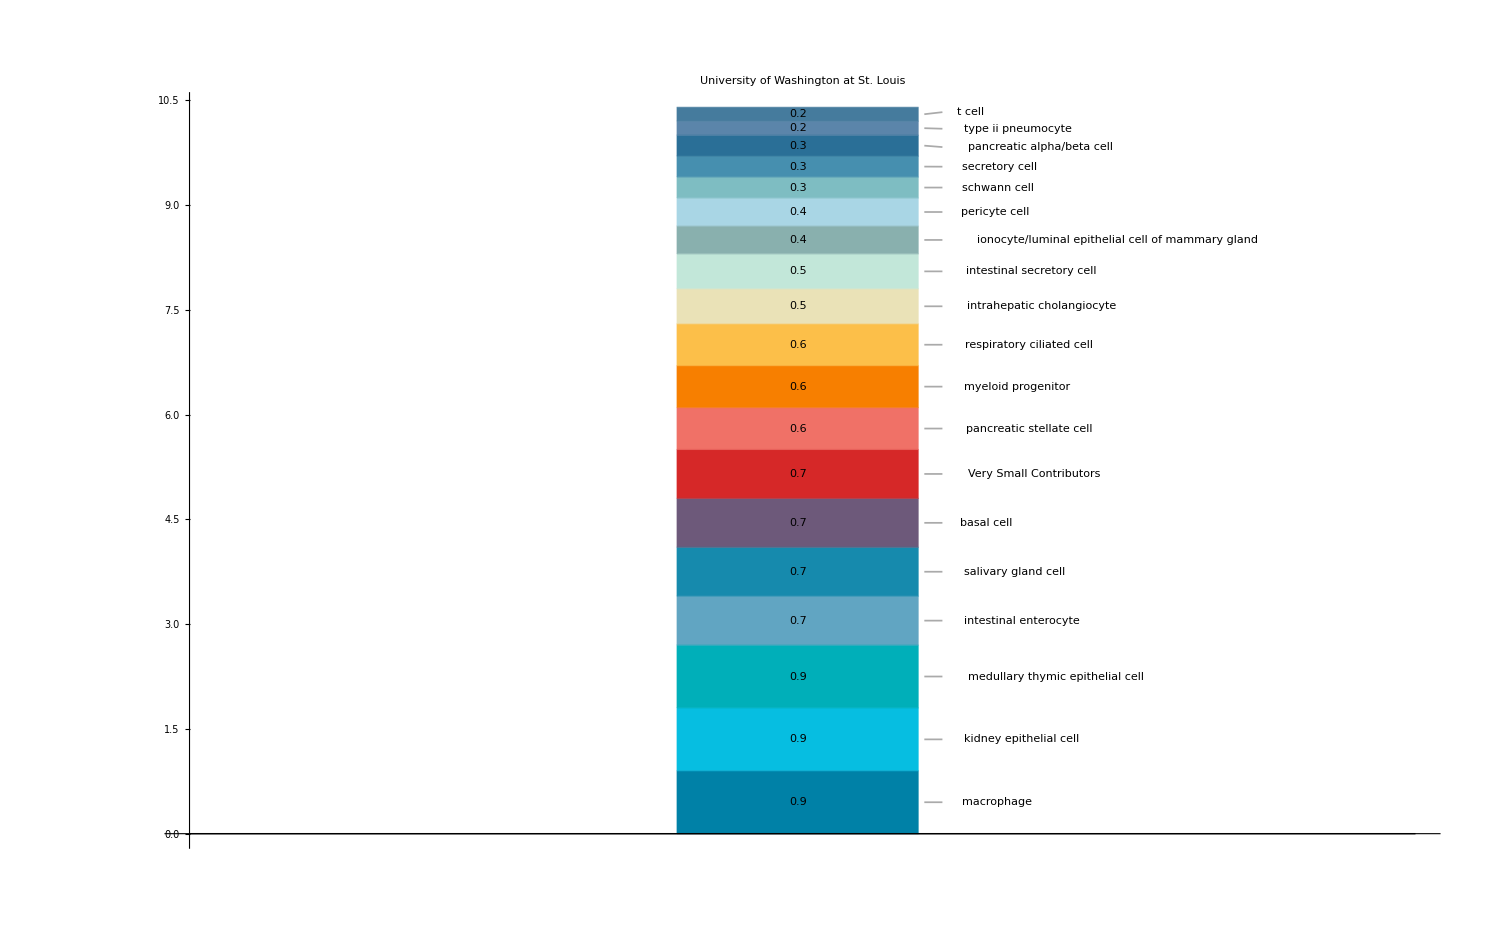

```mathematica
BarChart[shortlist,BarSpacing->2,ChartLayout->"Stacked",
ChartStyle-> barPal, ImageSize-> 1500, LabelingFunction ->( Placed[#1, Center]&), BaseStyle->{FontSize->15}, PlotLabel -> sampleCenter]
```

```mathematica
(* cool, now it's time to make the pie chart *)
```

```mathematica
gtPt1Percent = Position[Flatten[nonZeroVals], val_/;val  >=percentThresh ]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14}}

```mathematica
bigContribs = Part[nonZeroVals, #] &/@ gtPt1Percent
```

{{44.4},{10.4},{7.8},{4.6},{4.1},{3.2},{2.8},{2.7},{2.},{1.9},{1.7},{1.4},{1.4},{1.2}}

```mathematica
bigCells = Part[nonZeroCells, #] &/@ gtPt1Percent
```

{{erythrocyte/erythroid progenitor},{platelet},{monocyte},{nk cell},{b cell},{basophil},{mature conventional dendritic cell},{endothelial cell},{neutrophil},{cell of skeletal muscle},{adventitial cell},{thymocyte},{intestinal tuft cell},{salivary/bronchial secretory cell}}

```mathematica
bigTot = Total[Flatten[bigContribs]] ;
smallContribTot = Total[Flatten[goodSmallVals]];
bigTot + smallContribTot (* cool, so we sum to 1 between small and big contributions *)
```

100.

```mathematica
(* add the sum of the small contributions *)
```

```mathematica
bigContribs= AppendTo[bigContribs, {smallContribTot}];
bigCells = AppendTo[bigCells, {"Small"}]
```

{{erythrocyte/erythroid progenitor},{platelet},{monocyte},{nk cell},{b cell},{basophil},{mature conventional dendritic cell},{endothelial cell},{neutrophil},{cell of skeletal muscle},{adventitial cell},{thymocyte},{intestinal tuft cell},{salivary/bronchial secretory cell},{Small}}

```mathematica
Total[Flatten[bigContribs]]
```

100.

```mathematica
(* now it's time to sort it from big to small *)
```

```mathematica
finalOrderBig = Reverse[Ordering[bigContribs]];
bigContribs = Flatten[Part[bigContribs, #] &/@ finalOrderBig];
bigCells = Flatten[Part[bigCells, #] &/@ finalOrderBig];
```

```mathematica
(* make the labels for the pie chart *)
```

```mathematica
bigContribs
```

{44.4,10.4,10.4,7.8,4.6,4.1,3.2,2.8,2.7,2.,1.9,1.7,1.4,1.4,1.2}

```mathematica
test = Callout[bigContribs[[#]], bigCells[[#]],  Appearance -> "Leader"]&/@ Range[Length[bigCells]]
```

{Callout[44.4,erythrocyte/erythroid progenitor,Appearance→Leader],Callout[10.4,Small,Appearance→Leader],Callout[10.4,platelet,Appearance→Leader],Callout[7.8,monocyte,Appearance→Leader],Callout[4.6,nk cell,Appearance→Leader],Callout[4.1,b cell,Appearance→Leader],Callout[3.2,basophil,Appearance→Leader],Callout[2.8,mature conventional dendritic cell,Appearance→Leader],Callout[2.7,endothelial cell,Appearance→Leader],Callout[2.,neutrophil,Appearance→Leader],Callout[1.9,cell of skeletal muscle,Appearance→Leader],Callout[1.7,adventitial cell,Appearance→Leader],Callout[1.4,intestinal tuft cell,Appearance→Leader],Callout[1.4,thymocyte,Appearance→Leader],Callout[1.2,salivary/bronchial secretory cell,Appearance→Leader]}

```mathematica
"#84a98c"
```

#84a98c

```mathematica
piePal = Map [RGBColor,{"#bee9e8" ,"#62b6cb","#1b4965","#cae9ff","#5fa8d3",  "#a4508b", "#BC412B","#f26419","#f8c7cc", "#f7567c","#7e1946", "#f6ae2d", "#68b0ab","#84a98c", "#5bba6f", "#9ece9a", "#c8d5b9", "#355070","#6d597a","#b56576","#e56b6f","#eaac8b","#89b0ae",  "#457b9d","#555b6e","#6096ba"}]
```

{RGBColor[0.7450980392156863, 0.9137254901960784, 0.9098039215686274],RGBColor[0.3843137254901961, 0.7137254901960784, 0.796078431372549],RGBColor[0.10588235294117647, 0.28627450980392155, 0.396078431372549],RGBColor[0.792156862745098, 0.9137254901960784, 1.],RGBColor[0.37254901960784315, 0.6588235294117647, 0.8274509803921568],RGBColor[0.6431372549019608, 0.3137254901960784, 0.5450980392156862],RGBColor[0.7372549019607844, 0.2549019607843137, 0.16862745098039217],RGBColor[0.9490196078431372, 0.39215686274509803, 0.09803921568627451],RGBColor[0.9725490196078431, 0.7803921568627451, 0.8],RGBColor[0.9686274509803922, 0.33725490196078434, 0.48627450980392156],RGBColor[0.49411764705882355, 0.09803921568627451, 0.27450980392156865],RGBColor[0.9647058823529412, 0.6823529411764706, 0.17647058823529413],RGBColor[0.40784313725490196, 0.6901960784313725, 0.6705882352941176],RGBColor[0.5176470588235295, 0.6627450980392157, 0.5490196078431373],RGBColor[0.3568627450980392, 0.7294117647058823, 0.43529411764705883],RGBColor[0.6196078431372549, 0.807843137254902, 0.6039215686274509],RGBColor[0.7843137254901961, 0.8352941176470589, 0.7254901960784313],RGBColor[0.20784313725490197, 0.3137254901960784, 0.4392156862745098],RGBColor[0.42745098039215684, 0.34901960784313724, 0.47843137254901963],RGBColor[0.7098039215686275, 0.396078431372549, 0.4627450980392157],RGBColor[0.8980392156862745, 0.4196078431372549, 0.43529411764705883],RGBColor[0.9176470588235294, 0.6745098039215687, 0.5450980392156862],RGBColor[0.5372549019607843, 0.6901960784313725, 0.6823529411764706],RGBColor[0.27058823529411763, 0.4823529411764706, 0.615686274509804],RGBColor[0.3333333333333333, 0.3568627450980392, 0.43137254901960786],RGBColor[0.3764705882352941, 0.5882352941176471, 0.7294117647058823]}

```mathematica
PieChart[test, ChartStyle->piePal, SectorOrigin->{ Pi,1},BaseStyle->{FontSize->15},  ImageSize-> 1500,ImagePadding->{{240,60},{0,0}},LabelingFunction ->"RadialCenter", PlotLabel->sampleCenter]
```

-Graphics-

```mathematica
(* could try adding percents to the fractions but i wont *)
```

```mathematica
stringPercents = TextString[bigContribs[[#]]]<>"%" &/@ Range[Length[bigContribs]]
```

{44.4%,10.4%,10.4%,7.8%,4.6%,4.1%,3.2%,2.8%,2.7%,2.0%,1.9%,1.7%,1.4%,1.4%,1.2%}